## functions and settings

```mathematica
dataDir=FileNameJoin[{DirectoryName[NotebookDirectory[]]}]<>"\\outputs\\";
series=1;
subjectNum=24;
```

```mathematica
pxPerCm=63;
viewingDist=75;
pxToRadO=ArcTan[1/pxPerCm]/viewingDist;
pxToRad=pxToRadO;
pxToRad=1;


shapeSize=0.1/pxToRad;
cellNum=3;

dt=Join[ConstantArray[1/60,15],ConstantArray[3/50,5],ConstantArray[1/60,4]];
displayDimensions={1920,1080};
trackArea={{452,1476},{24,1044}}(*shape_size * cell_num/2, cell_num = 3, shape_size = 0.1/pxToRadO*)
```

{{452,1476},{24,1044}}

```mathematica
shapeSize
```

472.54

```mathematica
1080/2
```

540

```mathematica
0.1/pxToRadO
```

315.026

```mathematica
(*
BayesFactorOneSampleMean[data]
-data is a list of subject
-level means (e.g.percent correct),each a number in[0,1].
-We assume a Normal(mu,sigma^2) likelihood for each data[[i]].
-Prior:mu~Uniform(0..1),sigma~Jeffreys(1/sigma).
-Returns BF_10,i.e.p(Data|H1)/p(Data|H0).
*)BayesFactorOneSampleMean[data_List]:=Module[
{logLik,prior,pDataH1,pDataH0},

(*1) Log-likelihood of the entire sample given mu,sigma*)
logLik[mu_,sigma_]:=Sum[Log[PDF[NormalDistribution[mu,sigma],data[[i]]]],{i,1,Length[data]}];

(*2) Prior:Uniform in mu∈[0,1],Jeffreys(1/sigma) for sigma>0*)
prior[mu_,sigma_]:=If[0<=mu<=1&&sigma>0,1/sigma,0];

(*3) Marginal likelihood under H1:integrate over mu and sigma*)pDataH1=NIntegrate[Exp[logLik[mu,sigma]]*prior[mu,sigma],{mu,0,1},{sigma,0,∞},Method->{"LocalAdaptive"},Exclusions->None];

(*4) Marginal likelihood under H0:mu=0.5,integrate only over sigma*)
pDataH0=NIntegrate[Exp[logLik[0.5,sigma]]*prior[0.5,sigma],{sigma,0,∞},Method->{"LocalAdaptive"},Exclusions->None];

(*5) Bayes Factor BF_10*)
pDataH1/pDataH0
];
```

```mathematica
(*BayesFactorBetaBinomial-data:list of {k_i,N_i} pairs-alpha,beta:hyperparameters for the Beta prior (default 1,1->uniform) Returns:BF_10 (Bayes factor for H1:p~Beta(alpha,beta) vs.H0:p=0.5)*)
BayesFactorBetaBinomial[data_List,alpha_:1,beta_:1]:=Module[
{
(*Sum of successes and sum of all trials*)
sumK=Total[data[[All,1]]],
sumN=Total[data[[All,2]]],
(*Product of binomial coefficients for all subjects*)
prodBinom,pDataH1,pDataH0
},
(*Product of Binomial[n,k] for all pairs {k,n} in data*)
prodBinom=Product[Binomial[data[[i,2]],data[[i,1]]],{i,1,Length[data]}];
(*Marginal likelihood under H1 (beta-binomial)*)
pDataH1=prodBinom Beta[sumK+alpha,(sumN-sumK)+beta]/Beta[alpha,beta];
(*Marginal likelihood under H0 (p=0.5)*)
pDataH0=Product[Binomial[data[[i,2]],data[[i,1]]](1/2)^data[[i,2]],{i,1,Length[data]}];
(*Bayes Factor*)
N[pDataH1/pDataH0]
];

BayesFactorBetaBinomialOneSided[data_List,alpha_:1,beta_:1]:=Module[{(*Sum of successes and total trials across all data*)sumK=Total[data[[All,1]]],sumN=Total[data[[All,2]]],(*Product of binomial coefficients for all {k,n}*)prodBinom,pDataH1,pDataH0},(*1) Product of Binomial[n,k] over all subjects*)prodBinom=Product[Binomial[data[[i,2]],data[[i,1]]],{i,1,Length[data]}];
(*2) Marginal likelihood under H1:p in (0.5..1),prior~Beta(alpha,beta)*)(*Normally,beta-binomial integrates p from 0..1. For a one-sided test p>0.5,we only integrate from 0.5..1. This is the portion of the Beta distribution above 0.5.*)pDataH1=prodBinom*Beta[sumK+alpha,(sumN-sumK)+beta]/Beta[alpha,beta]*(1-BetaRegularized[0.5,sumK+alpha,(sumN-sumK)+beta]);
(*3) Marginal likelihood under H0:p=0.5 (fixed)*)pDataH0=Product[Binomial[data[[i,2]],data[[i,1]]]*(1/2)^(data[[i,2]]),{i,1,Length[data]}];
(*4) Bayes Factor BF_10 for "p>0.5" vs."p=0.5"*)N[pDataH1/pDataH0]];
```

## statistical learning

### data

```mathematica
subjectResponses=Table[
Flatten[Import[dataDir<>ToString[series]<>"\\"<>ToString[subject]<>"\\12\\subject_responses.csv"]]
,{subject,1,subjectNum}];
```

```mathematica
percentCorrects=Map[Mean,subjectResponses];
```

### learning performance

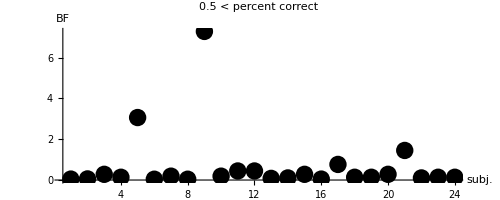

```mathematica
ListPlot[
Map[
BayesFactorBetaBinomialOneSided[{{Total[#],Length[#]}}]
&,subjectResponses
],PlotRange->All,AxesLabel->{"subj.","BF"},PlotLabel->"0.5 < percent correct",
PlotStyle->{PointSize->0.025,Black},AspectRatio->GoldenRatio[],ImageSize->500,PlotRange->{All,{0,8}}
]
```

```mathematica
learners={5,9,17,21};
```

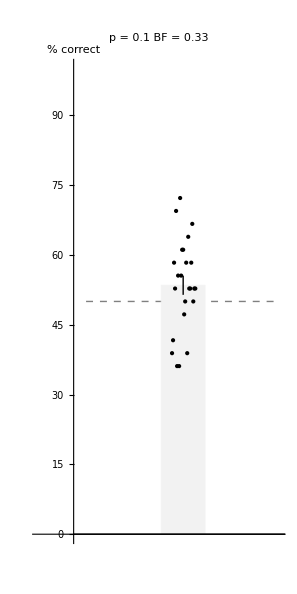

```mathematica
BarChart[
{100Mean[Map[Mean,subjectResponses]]},
PlotRange->{{-2,3},{0,100}},AspectRatio->2,ChartStyle->GrayLevel[0.95],AxesLabel->{None,"% correct"},
PlotLabel->"p = "<>ToString[Round[TTest[percentCorrects,0.5],0.01]] <>"\nBF = "<>ToString[Round[BayesFactorBetaBinomialOneSided[Map[
{Total[#],Length[#]}
&,subjectResponses
]],0.01]],
Prolog->{
Gray,Dashed,Line[{{-1,50},{3,50}}]
},
Epilog->{
Map[
Point,
Transpose[{
(1-0.5/2)+0.5Range[Length[subjectResponses]]/Length[subjectResponses],
100Map[Mean,subjectResponses]
}]
],
Thick,
Line[{
{1,100Mean[Map[Mean,subjectResponses]]-100StandardError[Map[Mean,subjectResponses]]},
{1,100Mean[Map[Mean,subjectResponses]]+100StandardError[Map[Mean,subjectResponses]]}
}]
}
]
```

## target tracking

### data

#### check

```mathematica
dataRaw=SortBy[Map[
{
ToExpression[StringSplit[#,"\\"][[-1]]],
GatherBy[Import[#<>"\\11\\data.txt","CSV"],First]
}&
,FileNames[All,dataDir<>ToString[series]<>"\\"]
],First][[All,2]];
```

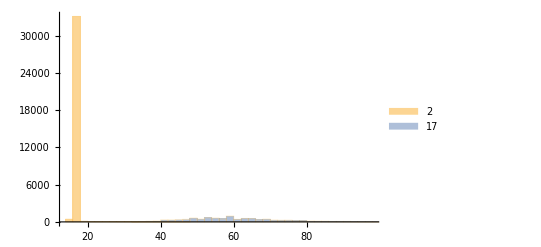

```mathematica
Histogram[
{
Differences[Drop[dataRaw[[2]],1][[All,1]][[All,1]]],
Differences[Drop[dataRaw[[17]],1][[All,1]][[All,1]]]
},{2},ChartLegends->{2,17}]
```

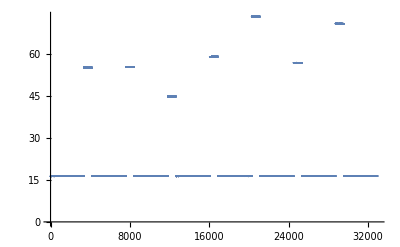

```mathematica
ListPlot[
MovingAverage[Differences[Drop[dataRaw[[15]],1][[All,1]][[All,1]]],825]
]
```

```mathematica
dt
```

{1/60,1/60,1/60,1/60,1/60,1/60,1/60,1/60,1/60,1/60,1/60,1/60,1/60,1/60,1/60,3/50,3/50,3/50,3/50,3/50}

```mathematica
Δt=10;
n=Δt/dt[[subject]];
```

600

```mathematica
tStart=0;
tEnd=60;
block=3;
Table[
Module[
{nStart,nEnd},
nStart=Round[tStart/dt[[subject]]]+1;
nEnd=Round[tEnd/dt[[subject]]];
nStart=1;
nEnd=Length[trackingRaw[[subject]][[block]]];
{
nEnd-nStart,
Graphics[
{
Gray,Line[trackingRaw[[subject]][[block]][[All,{2,3}]][[nStart;;nEnd]]],
Pink,Line[trackingRaw[[subject]][[block]][[All,{4,5}]][[nStart;;nEnd]]],
PointSize->0.0125,
Black,Point[trackingRaw[[subject]][[block]][[All,{2,3}]][[nStart;;nEnd]]],
Red,Point[trackingRaw[[subject]][[block]][[All,{4,5}]][[nStart;;nEnd]]]
},ImageSize->600,PlotRange->trackArea
]
}
],{subject,{10,16}}]//Row
```

```mathematica
trackArea
```

{{452,1476},{24,1044}}

```mathematica
300 /60
```

5

```mathematica
84 (3/50)//N
```

5.04

```mathematica
Min[displayDimensions]
```

1080

```mathematica
trackArea
```

{{},{}}

```mathematica
(72/alma[[All,2]])
```

{0.0174487,0.017055,0.0170743,0.0170732,0.0170641,0.0170465,0.0170571,0.0170571,0.0170424,0.017049,0.0170465,0.0170389,0.0170399,0.0170545,0.017049,0.0614138,0.061153,0.0608815,0.0612766,0.0614531}

```mathematica
1/60//N
```

0.0166667

```mathematica
(3/50)/(1/60)//N
```

3.6

```mathematica
Solve[Mean[alma[[16;;20]][[All,2]]]/Mean[alma[[1;;15]][[All,2]]]==dt/dt2,dt2]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{dt2→0.0597559}}

```mathematica
Rationalize[0.06]
```

3/50

```mathematica
dt//N
```

0.0166667

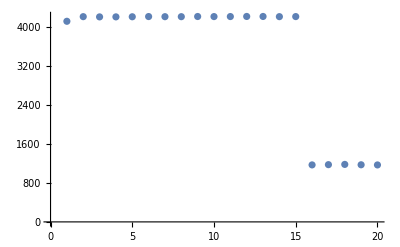

```mathematica
ListPlot[alma]
```

```mathematica
N[Mean[Map[Length,GatherBy[Drop[alma[[1]],1],First]]]]
```

4126.38

```mathematica
alma
```

{{1,4126.38},{2,4221.63},{3,4216.88},{4,4217.13},{5,4219.38},{6,4223.75},{7,4221.13},{8,4221.13},{9,4224.75},{10,4223.13},{11,4223.75},{12,4225.63},{13,4225.38},{14,4221.75},{15,4223.13},{16,1172.38},{17,1177.38},{18,1182.63},{19,1175.},{20,1171.63}}

```mathematica
1/(3/50)//N
```

16.6667

```mathematica
1/(1/60)//N
```

60.

#### prep

```mathematica
Map[
Module[
{filtered},
filtered=Import[#<>"\\11\\data.txt","CSV"][[All,{2,-4,-3,-2,-1}]];
Export[#<>"\\tracking.txt",filtered,"CSV"];
]
&,FileNames[All,dataDir<>ToString[series]<>"\\"]
];
```

```mathematica
Map[Length,tracking]
```

{33011,33773,33735,33737,33755,33790,33769,33769,33798,33785,33790,33805,33803,33774,33785,9379,9419,9461,9400,9373,2,2,2,2,2}

```mathematica
subject=23;
ListPlot[
{
GatherBy[tracking[[subject]],First][[1]][[All,{2,3}]][[100;;500]],
GatherBy[tracking[[subject]],First][[1]][[All,{4,5}]][[100;;500]]
},
PlotRange->trackArea,AspectRatio->1,Joined->True
]
```

GatherBy::list: List expected at position 1 in GatherBy[Drop[$Failed,1],First].

Part::partd: Part specification Drop[$Failed,1]⟦All,{2,3}⟧ is longer than depth of object.

Part::take: Cannot take positions 100 through 500 in Drop[$Failed,1]⟦All,{2,3}⟧.

GatherBy::list: List expected at position 1 in GatherBy[Drop[$Failed,1],First].

Part::partd: Part specification Drop[$Failed,1]⟦All,{4,5}⟧ is longer than depth of object.

Part::take: Cannot take positions 100 through 500 in Drop[$Failed,1]⟦All,{4,5}⟧.

General::prng: Value of option PlotRange -> {{},{}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
Table[
Table[
Table[
DistributionFitTest[Differences[GatherBy[tracking[[subject]],First][[block]][[All,col]]],NormalDistribution[],"PValue"],
{col,cols}],{cols,{{2,3},{4,5}}}]
,{subject,{2,17}}]
```

{{{5.10703×10^-15,5.21805×10^-15},{5.55112×10^-16,0.}},{{1.22125×10^-15,1.9984×10^-15},{0.,0.}}}

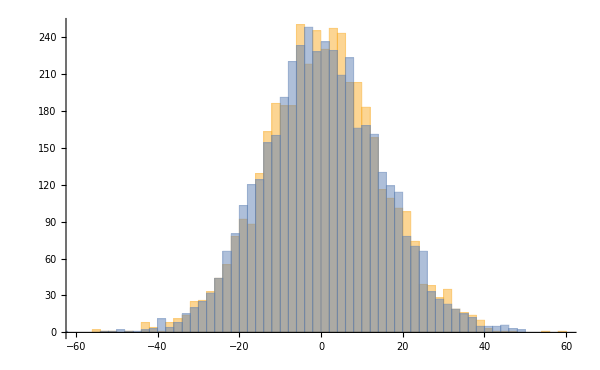
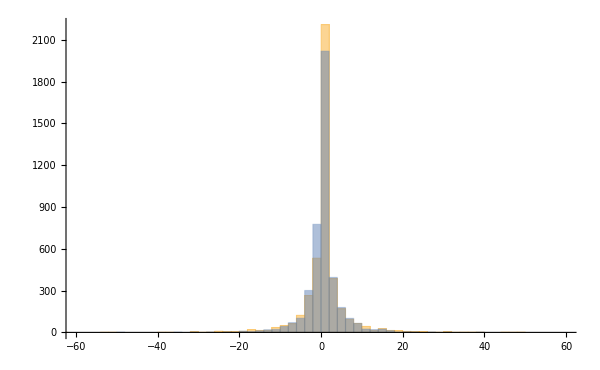
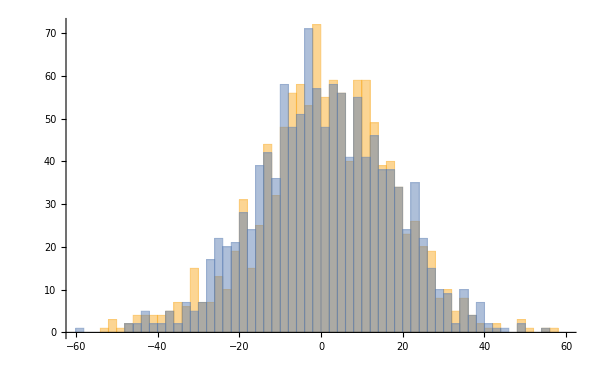
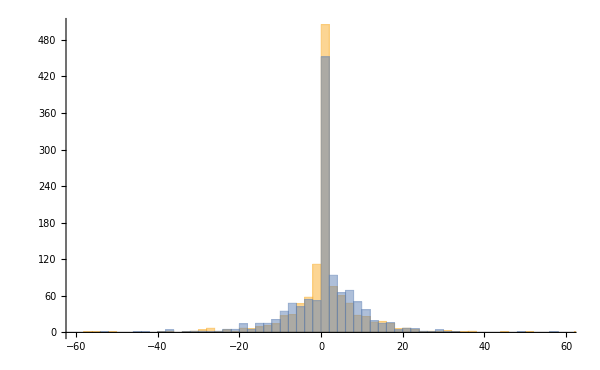

```mathematica
Table[
Table[
Histogram[
Table[
Differences[GatherBy[tracking[[subject]],First][[block]][[All,col]]],
{col,cols}],{2},ImageSize->600,PlotRange->{{-60,60},All}
],{cols,{{2,3},{4,5}}}]
,{subject,{2,17}}]
```

#### load

```mathematica
trackingHeader={"Block","Tracked_x","Tracked_y","Mouse_x","Mouse_y"};
tracking=Quiet[Table[
Drop[Import[dataDir<>ToString[series]<>"\\"<>ToString[subject]<>"\\tracking.txt","CSV"],1]
,{subject,1,subjectNum}]];
```

```mathematica
crossCorrelations=Quiet[Table[
Import[dataDir<>ToString[series]<>"\\"<>ToString[subject]<>"\\xcorr_by_block.json"]
,{subject,1,subjectNum}]];
```

```mathematica
MCMCResults=Quiet[Table[
Import[dataDir<>ToString[series]<>"\\"<>ToString[subject]<>"\\mcmc_summary_3.json"]
,{subject,1,subjectNum}]];
```

```mathematica
MCMCParameters={"action_cost","action_variability","sigma_cursor","sigma_target"};
```

```mathematica
parameterEstimations=Quiet[Table[
Map[Mean,MCMCParameters/.("MAP_estimates"/.MCMCResults[[subject]])]
,{subject,1,subjectNum}]];
```

```mathematica
rHats=Quiet[Table[
MCMCParameters/.("R_hat"/.MCMCResults[[subject]])
,{subject,1,subjectNum}]];
```

### trajectories

#### trajectories

```mathematica
2Mean[Flatten[Table[
Map[First,GatherBy[tracking[[subject]],First]][[All,{2,3}]]
,{subject,1,subjectNum}],1]]//N
```

{1917.58,1076.58}

```mathematica
Table[Table[
fun[Flatten[Table[
Map[fun[#[[All,col]]]&,GatherBy[tracking[[subject]],First]]
,{subject,1,subjectNum}]]]
,{fun,{Min,Max}}],{col,{2,3,4,5}}]//N
```

{{451.,1475.},{24.,1046.},{139.,1656.},{0.,1079.}}

```mathematica
trackArea={{452,1476},{24,1044}};
```

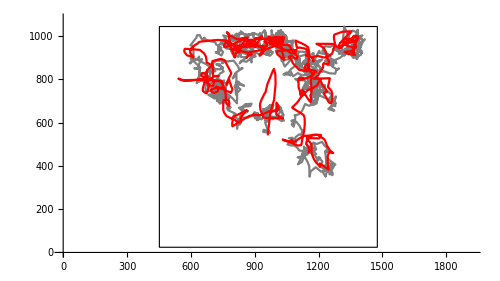
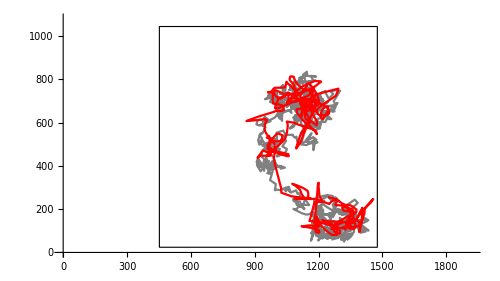
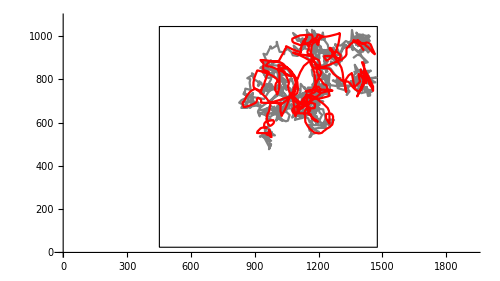
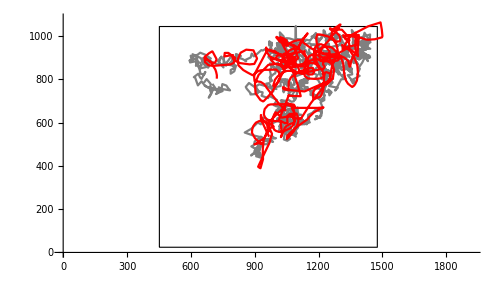
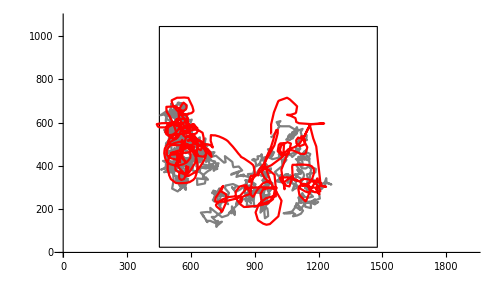
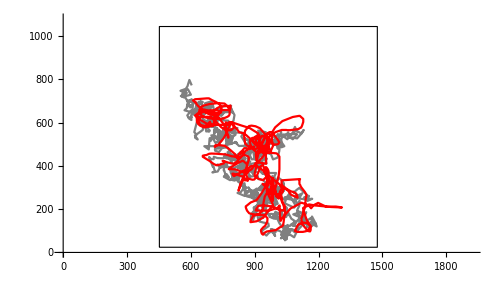
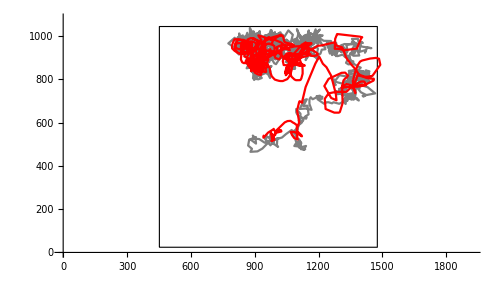
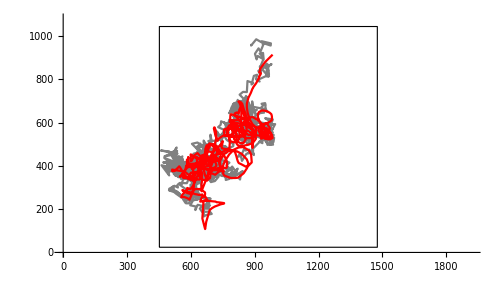

```mathematica
subject=17;
Table[
ListPlot[
 {
GatherBy[tracking[[subject]],First][[block]][[All,{2,3}]],
GatherBy[tracking[[subject]],First][[block]][[All,{4,5}]]
},
Joined->True,AspectRatio->displayDimensions[[2]]/displayDimensions[[1]],
PlotStyle->{Gray,Red},PlotRange->Transpose[{{0,0},displayDimensions}],ImageSize->500,
Prolog->{EdgeForm[{Black,Dashing[{Small,Small}]}],White,Rectangle[Transpose[trackArea][[1]],Transpose[trackArea][[2]]]}
],{block,1,8}]//Row
```

```mathematica
Table[ListPlot[
Map[
EuclideanDistance[#[[{2,3}]],#[[{4,5}]]]
&,GatherBy[tracking[[subject]],First][[block]]
],
AspectRatio->0.05,ImageSize->1200,Joined->True,PlotRange->All,PlotStyle->{Thin,Black}
],{block,1,8}]//Column
```

#### velocity

```mathematica
subject=1;
block=1;
```

```mathematica
dt//N
```

{0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.0166667,0.06,0.06,0.06,0.06,0.06}

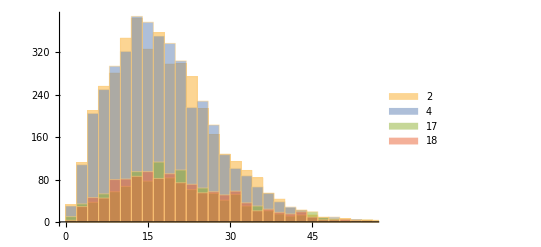

```mathematica
subjs={2,4,17,18};
Histogram[
Table[
Map[Sqrt[Total[#]]&,Differences[GatherBy[tracking[[subject]],First][[block]][[All,{2,3}]]]^2]//N
,{subject,subjs}],ChartLegends->subjs
]
```

### tracking

#### calc

```mathematica
targetNoise=pxToRad Map[
N[Mean[Map[StandardDeviation[Differences[#]]&,Transpose[#[[All,{2,3}]]]]]]
&,tracking];
```

```mathematica
trackingNoise=pxToRad Map[
N[Mean[Map[StandardDeviation[Differences[#]]&,Transpose[#[[All,{4,5}]]]]]]
&,tracking];
```

```mathematica
trackingPerformance=pxToRad Map[
N[Mean[Map[EuclideanDistance[#[[{2,3}]],#[[{4,5}]]]&,#]]]
&,tracking];
```

#### behaviour by block

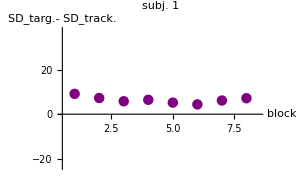
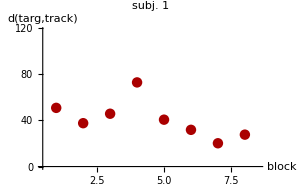
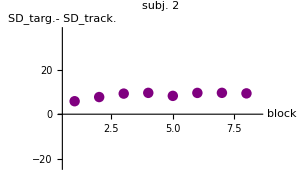
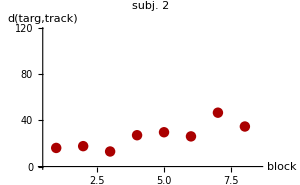
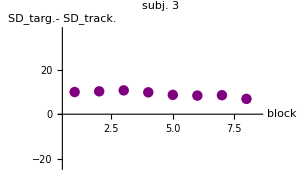
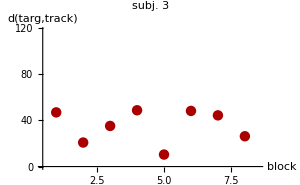
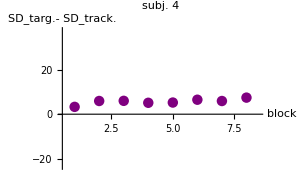
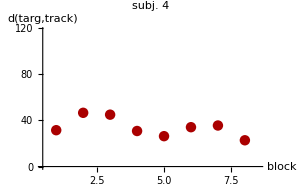
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Table[
Table[
ListPlot[
{
pxToRad Mean[{
 Map[StandardDeviation[Differences[#]]&,GatherBy[tracking[[subject]][[All,{1,5,3}]],First]]//#[[All,3]]-#[[All,2]]&,
 Map[StandardDeviation[Differences[#]]&,GatherBy[tracking[[subject]][[All,{1,4,2}]],First]]//#[[All,3]]-#[[All,2]]&
}],
Map[pxToRad EuclideanDistance[#[[{2,3}]],#[[{4,5}]]]&,GatherBy[tracking[[subject]],First]]
}[[type]],
PlotStyle->{{PointSize->0.025,Purple},{PointSize->0.025,Darker[Red]}}[[type]],
PlotRange->{{0.5,8.5}, {{-0.005,0.008},{0,0.025}}[[type]]/pxToRad},
PlotLabel->"subj. "<>ToString[subject],ImageSize->300,
AxesLabel->{"block",{"SD_targ.-\nSD_track.","d(targ,track)"}[[type]]}
]
,{type,1,2}]
,{subject,1,subjectNum}]//Grid
```

```mathematica
pxToRad Mean[{
Map[StandardDeviation[Differences[#]]&,GatherBy[tracking[[subject]][[All,{1,5,3}]],First]]//#[[All,3]]-#[[All,2]]&,
 Map[StandardDeviation[Differences[#]]&,GatherBy[tracking[[subject]][[All,{1,4,2}]],First]]//#[[All,3]]-#[[All,2]]&
}]//N
```

{5.77168,4.19866,7.36381,1.97051,3.65327,5.53994,5.29724,5.72483}

```mathematica
Map[pxToRad EuclideanDistance[#[[{2,3}]],#[[{4,5}]]]&,GatherBy[tracking[[subject]],First]]//N
```

{39.5374,48.0979,13.6144,92.4406,57.577,36.9082,26.6682,34.5234}

```mathematica
GatherBy[tracking[[subject]][[All,{1,5,3}]],First]//Dimensions
```

{7}

```mathematica
Table[ErrorListPlot[
{
Join[
{Range[8]},
Transpose[Map[
GetMeanAndSEM,
Transpose[Table[{
pxToRad Mean[{
Map[StandardDeviation[Differences[#]]&,GatherBy[tracking[[subject]][[All,{1,5,3}]],First]]//#[[All,3]]-#[[All,2]]&,
 Map[StandardDeviation[Differences[#]]&,GatherBy[tracking[[subject]][[All,{1,4,2}]],First]]//#[[All,3]]-#[[All,2]]&
}],
Map[pxToRad EuclideanDistance[#[[{2,3}]],#[[{4,5}]]]&,GatherBy[tracking[[subject]],First]]
}[[type]]
,{subject,1,subjectNum}]]
]]
]
},
 {{Purple,Darker[Red]}[[type]]},
{
PlotRange->{{0.5,8.5}, {{0,0.005},{0,0.02}}[[type]]/pxToRad},
AxesOrigin->{0.5,0},
PlotLabel->"mean and SEM across subjects",ImageSize->300,
AxesLabel->{"block",{"SD_targ.-\nSD_track.","d(targ,track)"}[[type]]}
},
{True,True,False}
],{type,1,2}]//Row
```

#### cross-correlograms

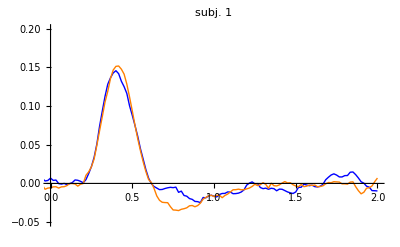
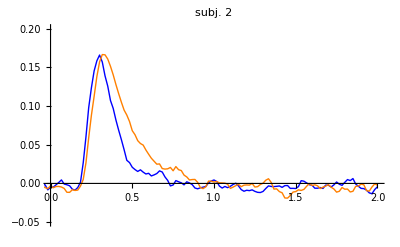
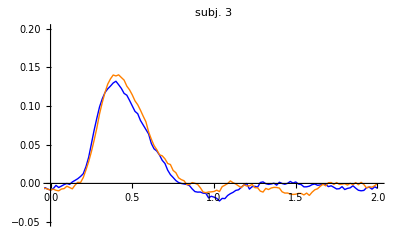
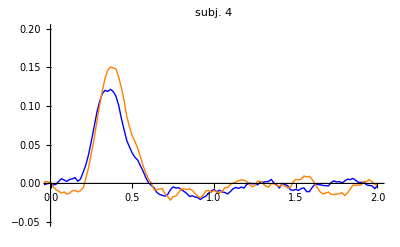
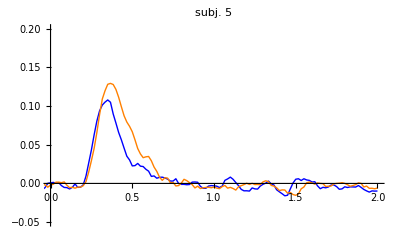
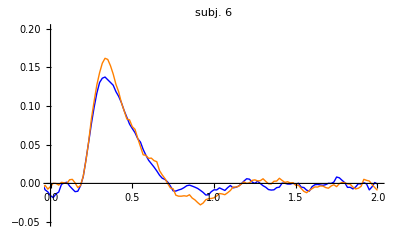
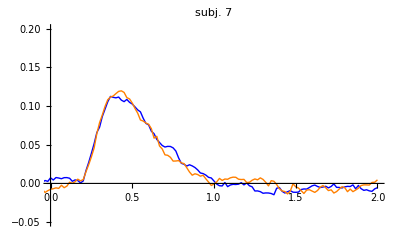
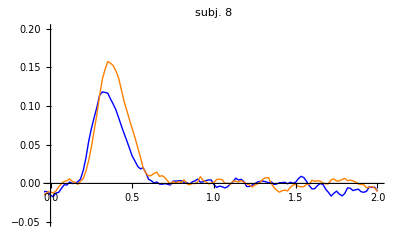

```mathematica
Table[
ListPlot[
Table[
Transpose[{
Range[-120,120]dt[[subject]],
Mean[dim/.crossCorrelations[[subject]]][[1]]
}]
,{dim,{"x_correls","y_correls"}}]
,Joined->True,PlotRange->{{0,2},{-0.05,0.2}},PlotStyle->{{Thick,Blue},{Thick,Orange}},PlotLabel->"subj. "<>ToString[subject]
],{subject,1,subjectNum}]
```

```mathematica
crossCorrPeaks=Table[SortBy[Transpose[{
Range[-120,120]dt[[subject]],
Mean[Table[Mean[dim/.crossCorrelations[[subject]]][[1]],{dim,{"x_correls","y_correls"}}]]
}],Last][[-1]],{subject,1,subjectNum}];
```

## both

```mathematica
subjectsToPlot=Range[subjectNum];
subjectsToPlot=Flatten[Position[dt,1/60]];
```

### tracking performance vs. percent correct

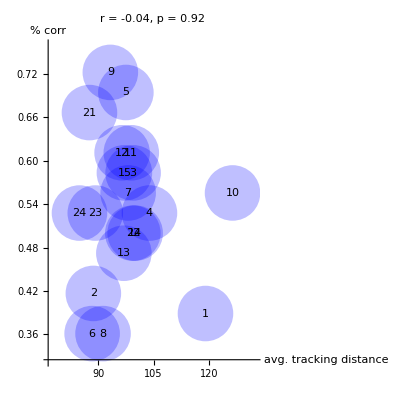

```mathematica
Module[
{data,corr,pVal,Rhat},
data=Transpose[{trackingPerformance[[subjectsToPlot]],percentCorrects[[subjectsToPlot]],subjectsToPlot}];
corr=Round[Correlation[data[[All,1]],data[[All,2]]],0.01];
pVal=Round[CorrelationTest[data[[All,{1,2}]]],0.01];
ListPlot[
data[[All,{1,2}]],PlotStyle->{PointSize->0.1,Opacity[0.25,Blue]},
PlotLabel->"r = "<>ToString[corr]<>", p = "<>ToString[pVal],
AxesLabel->{"avg. tracking\ndistance","% corr"},
AspectRatio->1,ImageSize->400,
PlotRange->{{Min[data[[All,1]]]0.9,Max[data[[All,1]]]1.05},{Min[data[[All,2]]]0.9,Max[data[[All,2]]]1.05}},
Epilog->Map[Text[#[[3]],#[[{1,2}]]]&,data]
]
]
```

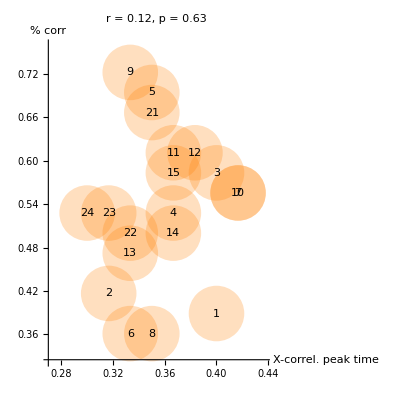

```mathematica
Module[
{data,corr,pVal,Rhat},
data=Transpose[{crossCorrPeaks[[All,1]][[subjectsToPlot]],percentCorrects[[subjectsToPlot]],subjectsToPlot}];
corr=Round[Correlation[data[[All,1]],data[[All,2]]],0.01];
pVal=Round[CorrelationTest[data[[All,{1,2}]]],0.01];
ListPlot[
data[[All,{1,2}]],PlotStyle->{PointSize->0.1,Opacity[0.25,Orange]},
PlotLabel->"r = "<>ToString[corr]<>", p = "<>ToString[pVal],
AxesLabel->{"X-correl.\npeak time","% corr"},
AspectRatio->1,ImageSize->400,
PlotRange->{{Min[data[[All,1]]]0.9,Max[data[[All,1]]]1.05},{Min[data[[All,2]]]0.9,Max[data[[All,2]]]1.05}},
Epilog->Map[Text[#[[3]],#[[{1,2}]]]&,data]
]
]
```

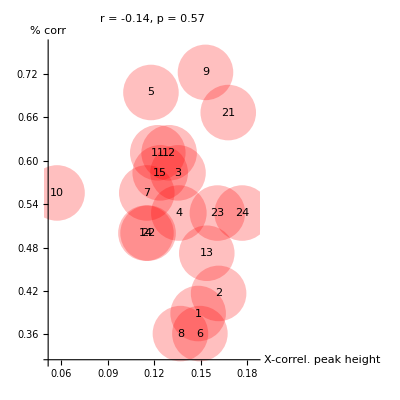

```mathematica
Module[
{data,corr,pVal,Rhat},
data=Transpose[{crossCorrPeaks[[All,2]][[subjectsToPlot]],percentCorrects[[subjectsToPlot]],subjectsToPlot}];
corr=Round[Correlation[data[[All,1]],data[[All,2]]],0.01];
pVal=Round[CorrelationTest[data[[All,{1,2}]]],0.01];
ListPlot[
data[[All,{1,2}]],PlotStyle->{PointSize->0.1,Opacity[0.25,Red]},
PlotLabel->"r = "<>ToString[corr]<>", p = "<>ToString[pVal],
AxesLabel->{"X-correl.\npeak height","% corr"},
AspectRatio->1,ImageSize->400,
PlotRange->{{Min[data[[All,1]]]0.9,Max[data[[All,1]]]1.05},{Min[data[[All,2]]]0.9,Max[data[[All,2]]]1.05}},
Epilog->Map[Text[#[[3]],#[[{1,2}]]]&,data]
]
]
```

### model

### fit parameters vs. summary stats

```mathematica
parameterLabels={"c_action","σ_action","σ_tracking","σ_target"};
```

```mathematica
Table[Table[
Module[
{data},
data=FilterOutliers[
Transpose[{
parameterEstimations[[subjectsToPlot]][[All,paramN]],
parameterEstimations[[subjectsToPlot]][[All,paramM]]
}],{2,2}];
ListPlot[
data,
PlotLabel->parameterLabels[[paramN]]<>", "<>parameterLabels[[paramM]],
ImageSize->250,AspectRatio->1,PlotStyle->{PointSize->0.02,Black}
]
],{paramM,1,4}],{paramN,1,4}]//Grid
```

```mathematica
parameterLabels
```

{c_action,σ_action,σ_tracking,σ_target}

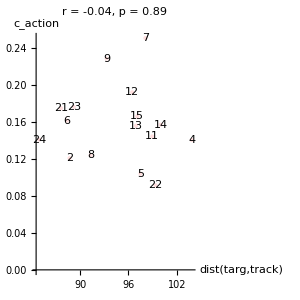
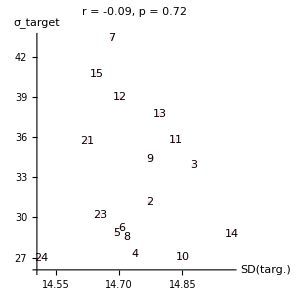
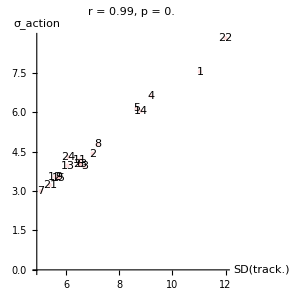

```mathematica
Table[
Module[
{paramN,data,corr,pVal,Rhat},
paramN={1,4,2}[[type]];
data=FilterOutliers[
Transpose[{
{trackingPerformance,targetNoise,trackingNoise}[[type]][[subjectsToPlot]],
parameterEstimations[[subjectsToPlot]][[All,paramN]]pxToRad,
subjectsToPlot
}],
{2,2,Infinity}
];
corr=Round[Correlation[data[[All,1]],data[[All,2]]],0.01];
pVal=Round[CorrelationTest[data[[All,{1,2}]]],0.01];
ListPlot[
data[[All,{1,2}]],PlotStyle->{PointSize->0.1,Opacity[0.25,Pink]},
PlotLabel->"r = "<>ToString[corr]<>", p = "<>ToString[pVal],
AxesLabel->{{"dist(targ,track)","SD(targ.)","SD(track.)"}[[type]],parameterLabels[[paramN]]},
AspectRatio->1,ImageSize->300,
(*PlotRange->{{Min[data[[All,1]]]0.9,Max[data[[All,1]]]1.05},{Min[data[[All,2]]]0.9,Max[data[[All,2]]]1.05}},*)
PlotRange->All,
Epilog->Map[Text[#[[3]],#[[{1,2}]]]&,data]
]
],{type,{1,2,3}}]//Row
```

```mathematica
trackingHeader
```

{Block,Tracked_x,Tracked_y,Mouse_x,Mouse_y}

```mathematica
targetNoiseDistributions=Map[
Map[Differences,Transpose[#[[All,{2,3}]]]]
&,tracking];
```

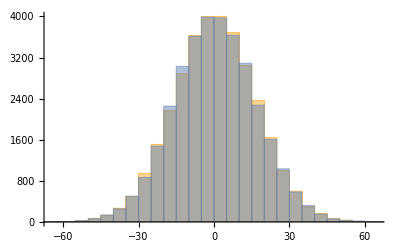
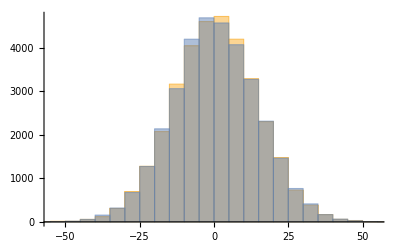
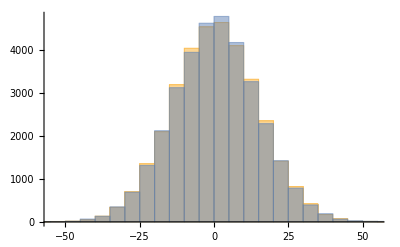
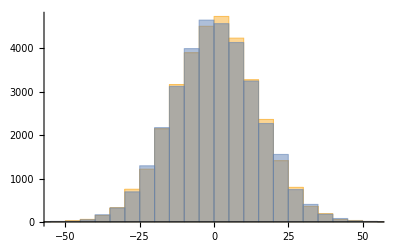

```mathematica
Map[Histogram,targetNoiseDistributions[[1;;4]]]
```

```mathematica
nonBoundedTargetNoiseDistribution=Module[
{imported},
imported=Drop[Import["C:\\Users\\Beno\\Documents\\CEU\\continuous_psychophysics\\vsl_with_tracking\\outputs\\no_bound\\1\\11\\data.txt","CSV"][[All,{2,-4,-3,-2,-1}]],1];
Map[Differences,Transpose[imported[[All,{2,3}]]]]
];
```

```mathematica
Map[DistributionFitTest[#,NormalDistribution[],"PValue"] &,nonBoundedTargetNoiseDistribution]
```

{1.85407×10^-14,1.80966×10^-14}

```mathematica
Table[
Join[{subject},Map[DistributionFitTest[#,NormalDistribution[],"PValue"] &,targetNoiseDistributions[[subject]]]]
,{subject,1,subjectNum}]//Grid
```

```mathematica
Map[Histogram,targetNoiseDistributions]
```

```mathematica
trackingNoiseDistributions=Map[
Map[Differences,Transpose[#[[All,{4,5}]]]]
&,tracking];
```

```mathematica
Map[Histogram,trackingNoiseDistributions]
```

### estimated parameters vs. VSL percent correct

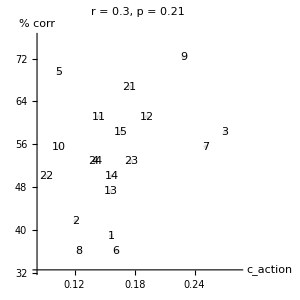
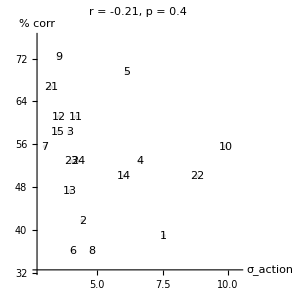
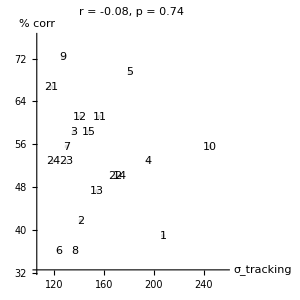

```mathematica
Table[
Module[
{data,corr,pVal,Rhat},
data=FilterOutliers[Transpose[{
parameterEstimations[[subjectsToPlot]][[All,paramN]]pxToRad,
100percentCorrects[[subjectsToPlot]],
rHats[[subjectsToPlot]][[All,paramN]],
subjectsToPlot
}],{3,Infinity,Infinity,Infinity}];
corr=Round[Correlation[data[[All,1]],data[[All,2]]],0.01];
pVal=Round[CorrelationTest[data[[All,{1,2}]]],0.01];
ListPlot[
data[[All,{1,2}]],PlotStyle->{PointSize->0.1,Opacity[0.25,Gray]},
PlotLabel->"r = "<>ToString[corr]<>", p = "<>ToString[pVal],AxesLabel->{parameterLabels[[paramN]],"% corr"},
AspectRatio->1,ImageSize->300,
PlotRange->{{Min[data[[All,1]]]0.9,Max[data[[All,1]]]1.05},{Min[data[[All,2]]]0.9,Max[data[[All,2]]]1.05}},
Epilog->Map[Text[#[[4]],#[[{1,2}]]]&,data]
]
],{paramN,1,3}]//Row
```